```mathematica
(*Dawid Bitner*)(*Algorytm roju cząstek*)ARC[f_,r_,N_,tMax_]:=Module[{x={},y,xb,yb, ,globalyb,globalxb,bests={},v={},i,j},(*Wyznaczenie N cząstek*)x=Table[{RandomReal[{r[[1]],r[[2]]}],RandomReal[{r[[1]],r[[2]]}]},{i,1,N}];
(*v w pierwszej iteracji=0*)v=Table[{0,0},{i,1,N}];
(*Wyznaczanie najlepszej pozycji w roju*)y=f[x[[1,1]],x[[1,2]]];
yb=y;
xb=x[[1]];
Do[y=f[x[[i,1]],x[[i,2]]];
If[y<yb,yb=y;
xb=x[[i]]];,{i,1,N}];
globalyb=yb;
globalxb=xb;
AppendTo[bests,yb];
Do[Do[(*Wyznaczanie prędkości*)v[[j,1]]=RandomReal[{0,1}]*v[[j,1]]+2*RandomReal[{0,1}]*(xb[[1]]-x[[j,1]])+2*RandomReal[{0,1}]*(globalxb[[1]]-x[[j,1]]);
v[[j,2]]=RandomReal[{0,1}]*v[[j,2]]+2*RandomReal[{0,1}]*(xb[[2]]-x[[j,2]])+2*RandomReal[{0,1}]*(globalxb[[2]]-x[[j,2]]);
(*Określenie nowego położenia cząsteczek*)x[[j,1]]=x[[j,1]]+v[[j,1]];
x[[j,2]]=x[[j,2]]+v[[j,2]];
(*Sprawdzanie czy pozaycja jest lepsza lokalnie*)y=f[x[[j,1]],x[[j,2]]];
If[y<yb,yb=y;
xb=x[[j]]];,{j,1,N}];
(*Sprawdzenie czy zosatła znaleziona lepsza pozycja*)If[yb<globalyb,globalyb=yb;
globalxb=xb;
AppendTo[bests,globalyb]];,{i,1,tMax}];
Print["Najlepszą wartość: ",globalyb,", ma osobnik: ",globalxb];
(*Wykres do zadania 3*)Print[ListPlot[bests,PlotLabel->"Przebieg zmiennośći najlepszej wartości",PlotRange->All]];];
```

```mathematica
SphereF[x_, y_]=x^2 + y^2;
Rosenbrock[x_,y_]= 100*(y-x^2)^2 + (1-x)^2;
```

Najlepszą wartość: 7.49161, ma osobnik: {3.73023,13.8953}

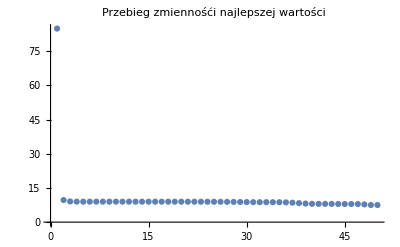

```mathematica
ARC[Rosenbrock,{-10,10}, 10, 100];
```

Najlepszą wartość: 0., ma osobnik: {1.,1.}

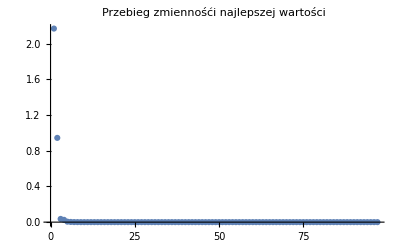

```mathematica
ARC[Rosenbrock,{-10,10}, 100, 1000];
```

Najlepszą wartość: 1.2579×10^-15, ma osobnik: {3.54668×10^-8,-2.05316×10^-11}

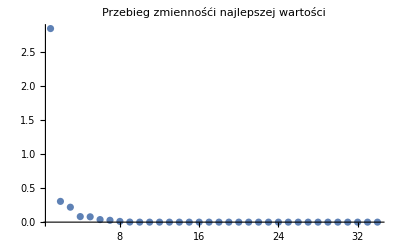

```mathematica
ARC[SphereF,{-10,10}, 10, 100];
```

Najlepszą wartość: 2.49274×10^-131, ma osobnik: {4.89392×10^-66,9.88389×10^-67}

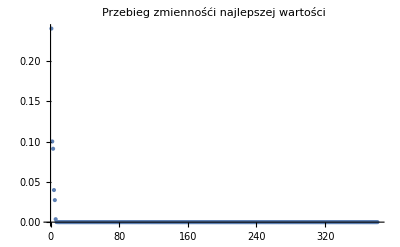

```mathematica
ARC[SphereF,{-10,10}, 100, 1000];
```